# ARIMA FORECAST

```mathematica
btc1=TimeSeries[FinancialData["BTC/USD",{{2020,10,17},{2021,10,17}}]];
logdata=TimeSeriesResample[btc1];

btc2=TimeSeries[FinancialData["BTC/USD",{{2020,10,24},{2021,10,24}}]];
logdata2=TimeSeriesResample[btc2];

btc3=TimeSeries[FinancialData["BTC/USD",{{2020,10,31},{2021,10,31}}]];
logdata3=TimeSeriesResample[btc3];

btc4=TimeSeries[FinancialData["BTC/USD",{{2020,11,7},{2021,11,7}}]];
logdata4=TimeSeriesResample[btc4];

btc5=TimeSeries[FinancialData["BTC/USD",{{2020,11,14},{2021,11,14}}]];
logdata5=TimeSeriesResample[btc5];

btc6=TimeSeries[FinancialData["BTC/USD",{{2020,11,21},{2021,11,21}}]];
logdata6=TimeSeriesResample[btc6];

btc7=TimeSeries[FinancialData["BTC/USD",{{2021,10,14},{2021,12,23}}]];
logdata7=TimeSeriesResample[btc7];
```

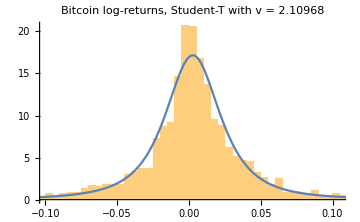

```mathematica
btc=FinancialData["BTC/USD",{2015}];
logreturn=Differences[Log[btc]];
Ret=logreturn[[2,1,1]];
dist=FindDistributionParameters[Ret,StudentTDistribution[a,b,c]];
d=dist[[1,2]];
e=dist[[2,2]];
f=dist[[3,2]];
Show[Histogram[Ret,100,"ProbabilityDensity"],Plot[PDF[StudentTDistribution[d,e,f],x],{x,-.5,.5},PlotRange->All],ImageSize->Medium,PlotLabel->StringTemplate["Bitcoin log-returns, Student-T with v = `2` "][freedom,m]]
freedom=f;
m=freedom;
student=StudentTDistribution[f];
tt = 7;
forecast=TimeSeriesForecast[TimeSeriesModelFit[logdata,"ARIMA"],{0,tt}];
forecast2=TimeSeriesForecast[TimeSeriesModelFit[logdata2,"ARIMA"],{0,tt}];
forecast3=TimeSeriesForecast[TimeSeriesModelFit[logdata3,"ARIMA"],{0,tt}];
forecast4=TimeSeriesForecast[TimeSeriesModelFit[logdata4,"ARIMA"],{0,tt}];
forecast5=TimeSeriesForecast[TimeSeriesModelFit[logdata5,"ARIMA"],{0,tt}];
forecast6=TimeSeriesForecast[TimeSeriesModelFit[logdata6,"ARIMA"],{0,tt}];

q[ci_]:=InverseSurvivalFunction[StudentTDistribution[f],1-(1-ci)/2];

se=Sqrt[forecast["MeanSquaredErrors"]];
se2=Sqrt[forecast2["MeanSquaredErrors"]];
se3=Sqrt[forecast3["MeanSquaredErrors"]];
se4=Sqrt[forecast4["MeanSquaredErrors"]];
se5=Sqrt[forecast5["MeanSquaredErrors"]];
se6=Sqrt[forecast6["MeanSquaredErrors"]];

tsci[ci_,u_]:=TimeSeriesThread[{1,u q[ci]}.#&,{forecast,se}];
tsci2[ci_,u_]:=TimeSeriesThread[{1,u q[ci]}.#&,{forecast2,se2}];
tsci3[ci_,u_]:=TimeSeriesThread[{1,u q[ci]}.#&,{forecast3,se3}];
tsci4[ci_,u_]:=TimeSeriesThread[{1,u q[ci]}.#&,{forecast4,se4}];
tsci5[ci_,u_]:=TimeSeriesThread[{1,u q[ci]}.#&,{forecast5,se5}];
tsci6[ci_,u_]:=TimeSeriesThread[{1,u q[ci]}.#&,{forecast6,se6}];

Manipulate[DateListPlot[{logdata7,forecast,forecast2 ,forecast3,forecast4,forecast5,forecast6,tsci[ci,1],tsci[ci,-1],tsci2[ci,1],tsci2[ci,-1],tsci3[ci,1],tsci3[ci,-1],tsci4[ci,1],tsci4[ci,-1],tsci5[ci,1],tsci5[ci,-1],tsci6[ci,1],tsci6[ci,-1]},Filling->{8->{9},{10->{11}},{12->{13}},{14->{15}},{16->{17}},{18->{19}}},PlotLegends->LineLegend[{Red,Black,{Red,Dashed}},{"Predicted","Actual","Confidence"}],PlotStyle->{{Black,Thick},Red,Red,Red,Red,Red,Red,{Red,Dashed},{Red,Dashed},{Red,Dashed},{Red,Dashed},{Red,Dashed},{Red,Dashed},{Red,Dashed},{Red,Dashed},{Red,Dashed},{Red,Dashed},{Red,Dashed},{Red,Dashed}},PlotRange->Automatic,PlotLabel->StringTemplate["Forecast for `3` days"][freedom,m,tt],PlotLabel->LineLegend[{Red,Black,{Red,Dashed}},{"Predicted","Actual","Confidence"}]],{ci,{.68,.75,.95,.98,.998}}]
```

```mathematica
bitc=QuantityMagnitude[logdata7];
Clear[n,o,p];proc=EstimatedProcess[bitc["Values"],GeometricBrownianMotionProcess[n,o,p]];
paths=RandomFunction[proc,{bitc["PathLength"],bitc["PathLength"]+14,1},200];
td=TemporalData[paths["ValueList"],{logdata7["LastDate"],Automatic,"Day"},ValueDimensions->1];
pp=DateListPlot[td,Joined->True,PlotLabel->LineLegend[{Red,Dashed},{"Brownian"}],PlotStyle->Directive[Opacity[.08]]];
mF=TimeSeriesThread[Mean,td];

DynamicModule[{ci=0.68},fore3=DateListPlot[{logdata7,forecast,forecast2,forecast3,forecast4,forecast5,forecast6,tsci[ci,1],tsci[ci,-1],tsci2[ci,1],tsci2[ci,-1],tsci3[ci,1],tsci3[ci,-1],tsci4[ci,1],tsci4[ci,-1],tsci5[ci,1],tsci5[ci,-1],tsci6[ci,1],tsci6[ci,-1]},Filling->{8->{9},{10->{11}},{12->{13}},{14->{15}},{16->{17}},{18->{19}}},PlotLabels->{None,"Predicted",None,None,None,None,None,"68%",None,None,None,None},PlotStyle->{{Black,Thick,Thickness[.003]},{Red,Thickness[.002]},{Red,Thickness[.002]},{Red,Thickness[.002]},{Red,Thickness[.002]},{Red,Thickness[.002]},{Red,Thickness[.002]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]}}]];

DynamicModule[{ci=0.90},fore1=DateListPlot[{logdata7,forecast,forecast2,forecast3,forecast4,forecast5,forecast6,tsci[ci,1],tsci[ci,-1],tsci2[ci,1],tsci2[ci,-1],tsci3[ci,1],tsci3[ci,-1],tsci4[ci,1],tsci4[ci,-1],tsci5[ci,1],tsci5[ci,-1],tsci6[ci,1],tsci6[ci,-1]},Filling->{8->{9},{10->{11}},{12->{13}},{14->{15}},{16->{17}},{18->{19}}},PlotLabels->{None,None,None,None,None,None,None,"90%",None,None,None,None},PlotStyle->{{Black,Thick,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]}}]];

DynamicModule[{ci=0.95},fore2=DateListPlot[{logdata7,forecast,forecast2,forecast3,forecast4,forecast5,forecast6,tsci[ci,1],tsci[ci,-1],tsci2[ci,1],tsci2[ci,-1],tsci3[ci,1],tsci3[ci,-1],tsci4[ci,1],tsci4[ci,-1],tsci5[ci,1],tsci5[ci,-1],tsci6[ci,1],tsci6[ci,-1]},Filling->{8->{9},{10->{11}},{12->{13}},{14->{15}},{16->{17}},{18->{19}}},PlotLabels->{None,None,None,None,None,None,None,"95% Confidence",None,None,None,None},PlotStyle->{{Black,Thick,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]},{Red,Thickness[-2]}}]];
```

```mathematica
Show[DateListPlot[bitc,PlotRange->{{bitc["FirstTime"],td["LastTime"]},{Min[30000],Max[100000]}},Joined->True,PlotStyle->Thickness[-2]],pp,DateListPlot[mF,Joined->True,PlotStyle->Directive[Thick,Gray],PlotLabels->"Brownian"],fore1,fore2,fore3,ListPlot[logdata7,PlotStyle->{Black,Opacity[.7]},PlotMarkers->{Automatic, Small}],ImageSize->Large]
```

## Time Series Analysis

Stationarity Test

```mathematica
urt=UnitRootTest[Ret,Automatic,"HypothesisTestData"]
```

HypothesisTestData[…]

```mathematica
urt["TestDataTable",All]
```

| Statistic | P-Value
Dickey-Fuller F | -2238.31 | 5.0505×10^-20
Dickey-Fuller T | -47.4373 | 2.03607×10^-22
Phillips-Perron F | -2274.8 | 4.42822×10^-20
Phillips-Perron T | -47.4377 | 2.03578×10^-22

```mathematica
DecimalForm[%]
```

| Statistic | P-Value
Dickey-Fuller F | -2172.7 | 0.0000000000000000000643245
Dickey-Fuller T | -46.7079 | 0.000000000000000000000260729
Phillips-Perron F | -2209.12 | 0.0000000000000000000561926
Phillips-Perron T | -46.71 | 0.00000000000000000000026054

P-Value > .05, Failure to reject H_0, data is has a unit root and is non-stationary

Autocorrelation Test

```mathematica
act=AutocorrelationTest[Ret,Automatic,"HypothesisTestData"]
```

HypothesisTestData[…]

```mathematica
act["TestDataTable", All]
```

| Statistic | P-Value
Box-Pierce | 8.39619 | 0.395756
Ljung-Box | 8.42403 | 0.393182

P Values typically large when no autocorrelation

```mathematica
btc8=TimeSeries[FinancialData["BTC/USD",{{2016,11,20},{2021,11,19}}]];
logdata8=TimeSeriesResample[btc8];
```

```mathematica
v = btc8[[2,1,1]];
```

```mathematica
quad=Fit[v,{1,x,x^2},x]
```

9993.74-31.7785 x+0.0303052 x^2

```mathematica
quart=Fit[v,{1,x,x^2,x^3,x^4,x^5},x]
```

1486.37-27.6085 x+0.254012 x^2-0.000492932 x^3+3.50157×10^-7 x^4-8.04371×10^-11 x^5

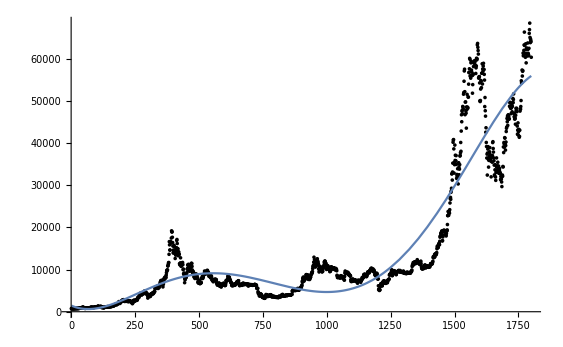

```mathematica
Show[ListPlot[v,PlotStyle->Black],Plot[{quart},{x,1,Length[v]}]]
```